# 1. DN - Računalniška orodja v matematiki

#### 1. Analiza z mathematico

Točke od a do j rešite točno in tudi numerično.

a. Definirajte funkcijo .

```mathematica
f[x_] = (E^ (x+3)) / (100*x + 2)
```

ⅇ^(3+x)/(2+100 x)

b. Izračunajte definicijsko območje funkcije .

```mathematica
FunctionDomain[f[x],x]
```

x<-1/50||x>-1/50

c. Izračunajte limite funkcije  na robovih definicijskega območja.

```mathematica
Limit[f [x],x-> -1/50, Direction->"FromBelow"]
```

-∞

```mathematica
Limit[f[x], x -> -1/50, Direction->"FromAbove"]
```

∞

```mathematica
Limit[f[x], x -> Infinity]
```

∞

```mathematica
Limit[f[x], x -> -Infinity]
```

0

d. Izračunajte odvod funkcije .

```mathematica
f'[x]
```

-(100 ⅇ^(3+x))/(2+100 x)^2+ⅇ^(3+x)/(2+100 x)

e. Izračunajte lokalne ekstreme funkcije .

```mathematica
Solve[D[f[x],x]==0,x]
```

{{x→49/50}}

f. Izračunajte intervale naraščanja in padanja funkcije .

```mathematica
Reduce[f'[x] > 0, x]
Reduce[f'[x] < 0, x]
```

x>49/50

x<-1/50||-1/50<x<49/50

g. Narišite graf funkcije  na intervalu [-5, 5].

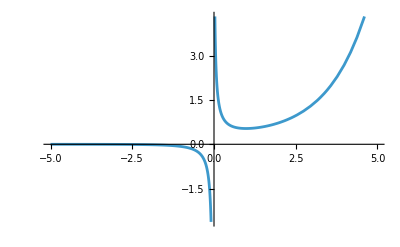

```mathematica
Plot[f[x], {x, -5, 5}]
```

h. Določite zalogo vrednosti funkcije .

```mathematica
FunctionRange[f[x],x,y]
```

y<0||y≥ⅇ^(199/50)/100

i. Izračunajte nedoločeni integral funkcije .

```mathematica
Integrate[f[x],x]
```

1/100 ⅇ^(149/50) ExpIntegralEi[1/50+x]

j. Na 3 decimalke natančno izračunajte volumen vrtenine , ki jo dobimo, če graf funkcije  zavrtimo okoli  osi na intervalu [0.5, 2]. Vrtenino tudi narišite.

```mathematica
RevolutionPlot3D[f[x], {x, 0.5, 2}]
```

-Graphics3D-

```mathematica
Integrate[Pi f[x]^2,{x,0.5,2}]
```

1.66479

#### 2. Splošno o mathematici

a. Pobrišite vrednost vseh spremenljivk, ki ste jih uporabili v prejšnji nalogi.

b. Definirajte funkcijo  in izračunajte njeno vrednost v vseh celih številih med 1 in 100.

c.  Iz seznama dobljenega v nalogi b. izberite zgolj tiste vrednosti, ki imajo na mestu enic praštevilo. Pomagajte si s _?PrimeQ in MemberQ.

d. Definirajte anonimno funkcijo, ki kvadrira število in mu prišteje 1 in jo uporabite na zgoraj dobljenem seznamu.

e. Seznam iz prejšnje naloge zaokrožite navzdol in seštejte vsa tista števila, ki so deliva s 3.

#### 3. Prepisovalna pravila

```mathematica
Clear[x, y, izraz]
izraz = x^2 + 2x + 1
```

a. Definirajte prepisovalno pravilo, ki  v izrazu vse pojavitve x zamenja z y + 1.

b. Z uporabo prepisovalnih pravil izračunajte vrednost izraza za  x = 2

c. Definirajte funkcija  in s pomočjo prepisovalnih pravil zamenjajte vse pojavitve  v

d. Prepisovalno pravilo iz naloge c uporabite na funkciji ,  kolikokrat gre.

e. Definiraj prepisovalna pravila, s pomočjo katerih lahko izračunate poljuben člen fibonaccijevega zaporedja, z začetkom `Fib[10]`